```mathematica
householdMin=Log10@{1,64,1*10^3,128*10^3,2*10^6,4*10^6};
householdMax=Log10@{16,10^3,64*10^3,2*10^6,16*10^6,64*10^6};
researchMin=Log10@{16,10^3,16*10^3,10^6,8*10^6,16*10^6};
researchMax=Log10@{128,16*10^3,256*10^3,8*10^6,64*10^6,128*10^6};
expensiveResearchMin=Log10@{128,16*10^3,128*10^3,4*10^6,32*10^6,64*10^6};
expensiveResearchMax=Log10@{10^3,64*10^3,10^6,32*10^6,512*10^6,2*10^9};

years={1970,1980,1990,2000,2010,2020};
```

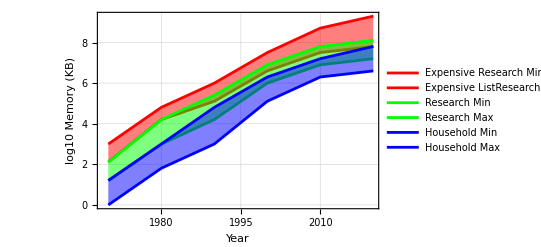

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/REVIEW/computer_memory.png

```mathematica
household=Transpose[{years,householdMin,householdMax}];
research=Transpose[{years,researchMin,researchMax}];
expensiveResearch=Transpose[{years,expensiveResearchMin,expensiveResearchMax}];
opt={
PlotRange->All,
GridLines->Automatic,
PlotStyle->{Black},
Frame->True,
FrameTicksStyle->Directive[Black,12],
FrameStyle->Directive[Black,12],
FrameLabel->{"Year","log10 Memory (KB)"},
FrameTicks->{Automatic,Automatic},
AxesStyle->{Black}
};
Show[
ListPlot[{expensiveResearch[[All,{1,2}]],expensiveResearch[[All,{1,3}]]},Filling->{1->{2}},Joined->True,PlotStyle->{Red,Red},FillingStyle->Directive[Opacity[0.5],Red],PlotLegends->{"Expensive Research Min","Expensive ListResearch Max"},Evaluate[opt]],
ListPlot[{research[[All,{1,2}]],research[[All,{1,3}]]},Filling->{1->{2}},Joined->True,PlotStyle->{Green,Green},FillingStyle->Directive[Opacity[0.5],Green],PlotLegends->{"Research Min","Research Max"},Evaluate[opt]],
ListPlot[{household[[All,{1,2}]],household[[All,{1,3}]]},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Blue},FillingStyle->Directive[Opacity[0.5],Blue],PlotLegends->{"Household Min","Household Max"},Evaluate[opt]],
Background->None]
Export[NotebookDirectory[]<>"computer_memory.png",%,Background->Lighter[White, 0.5]]
```